# Ejercicio 1 - TP5

Pablo Chehade
First version: 2021/11/02 (mi cumpleaños xd)

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Defino la función ListaRandom que devuelve la posición (x,y) dada por x e y enteros entre min y max random de NRandom puntos.Pisar indica si la lista que retorna puede tener valores idénticos*)
ListaRandom[NRandom_,min_,max_,pisar_]:=Module[{Lista},
(*para implementar pisar seguro será útil;
DeleteDuplicates[list]
*)
Lista =ConstantArray[0,{NRandom,2}];
Do[
Do[
Lista⟦j,k⟧ = RandomInteger[{min,max}]
,{j,1,NRandom}];
,{k,1,2}];
Lista];
(*test de la función;
Print[ListaRandom[10,1,5,True]]
*)
```

```mathematica
(*Defino función pos que se encarga de hacer el arreglo periódico automáticamente*)
pos[k_,J_]:=If[Mod[k,J-1]≠0,Mod[k,J-1],J-1];
(*k es la posición y J el tamaño del arreglo periódico*)
```

```mathematica
(*Defino función RandomWalk que toma una posición (x,y) dada por x e y enteros y retorna aleatoriamente una (x+1,y),(x-1,y),(x,y+1) o (x,y-1)*)
RandomWalk[{x_,y_},NMalla]:=Module[{k,xnew,ynew},
xnew = x; ynew = y;
k = RandomInteger[{1,4}];
(*Print["k = ", k];*)
Switch[k,
1, xnew = pos[xnew + 1,NMalla], (*derecha*)
2,xnew = pos[xnew - 1,NMalla], (*izquierda*)
3,ynew = pos[ynew + 1,NMalla], (*arriba*)
4,ynew = pos[ynew-1,NMalla]]; (*abajo*)
{xnew,ynew}]
(*Test de función;
NMalla = 10;
Print[RandomWalk[{2,2},NMalla]]
*)
```

```mathematica
(*Defino función Criterio que toma malla,ListParticle y ListSeed,evalúa si alguna partícula de ListParticles es vecina cercana de alguna de ListSeed.En caso afirmativo,la pinta de Seed, la saca de ListParticles y la agrega a ListSeed*)
Criterio[malla_, NMalla_,ListParticles_, ListSeed_]:=Module[{suma, ListParticlesnew, ListSeednew,mallanew,  dropeo,x,y},
ListParticlesnew = ListParticles; ListSeednew = ListSeed; mallanew = malla;
dropeo = 0; (*cantidad de Particles que se convirtieron en Seed*)
Do[
{x,y} = ListParticles⟦j⟧;
suma =malla⟦pos[x+1,NMalla],y⟧ + 
malla⟦pos[x+1,NMalla],pos[y+1,NMalla]⟧ +
malla⟦x,pos[y+1,NMalla]⟧ + 
malla⟦pos[x-1,NMalla],pos[y+1,NMalla]⟧+ 
malla⟦pos[x-1,NMalla],y⟧ + 
malla⟦pos[x-1,NMalla],pos[y-1,NMalla]⟧ + 
malla⟦x,pos[y-1,NMalla]⟧  + 
malla⟦pos[x+1,NMalla],pos[y-1,NMalla]⟧ ;
If[suma ≠ 0,
mallanew⟦x,y⟧ = 1;
ListParticlesnew=Drop[ListParticlesnew,{j+dropeo}];
dropeo++;
AppendTo[ListSeednew,ListParticles⟦j⟧ ]
 ]
,{j,1,Length[ListParticles]}];
{mallanew,ListParticlesnew,ListSeednew}
]
```

8

{{1,5}}

{{5,6},{8,6},{1,2},{7,5},{1,1}}

holanda

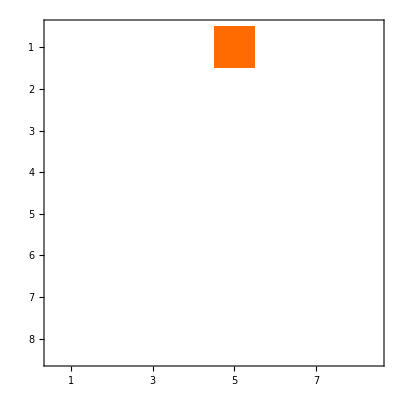

Part::partw: Part 9 of {{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partd1: Depth of object {{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}} is not sufficient for the given part specification.

General::stop: Further output of Part::partd1 will be suppressed during this calculation.

Part::partd: Part specification {{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}⟦0,1⟧ is longer than depth of object.

Part::partd: Part specification {{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}⟦0,2⟧ is longer than depth of object.

Part::partd: Part specification {{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}⟦0,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{5,6},{8,6},{1,2},{7,5},{1,1}},{{1,5}}}

-Graphics-

Frame[{{1,5}},{{5,6},{8,6},{1,2},{7,5},{1,1}}]

```mathematica
pot=3;(*potencia de 2*)
NMalla=2^pot;
Print[NMalla]
(*Creo una matriz malla Nmalla x Nmalla de ceros*)
malla = ConstantArray[0,{NMalla,NMalla}];
(*para graficar:;
MatrixPlot[malla]
*)
(*Al azar elijo algunos elementos que serán la semilla,recordemos que no se pueden pisar*)
NSeed = 1;
ListSeed = ListaRandom[NSeed,1,NMalla,False]
(*Al azar elijo algunos elementos que serán las partículas difusivas,recordemos que se pueden pisar*)
NParticles = 5;
ListParticles = ListaRandom[NParticles,1,NMalla,True]

Print["holanda"]
(*Pinto la matriz malla con un 1 si es Particle o un 2 si es Seed*)
Do[
malla⟦ListParticles⟦j,1⟧ ,ListParticles⟦j,2⟧⟧ = 0;
,{j,1,NParticles}]
Do[
malla⟦ListSeed⟦j,1⟧ ,ListSeed⟦j,2⟧⟧ = 1;
,{j,1,NSeed}]

MatrixPlot[malla]

{malla, ListParticles, ListSeed} = Criterio[malla,ListParticles,ListSeed]

MatrixPlot[malla]

(*Defino frame que indica la evolución temporal*)
Frame[ListSeed,ListParticles]
(*Recorro ListParticles y a cada una de ellas les aplico RandomWalk*)

(*Evalúo*)
```